```mathematica
data = Import["/net/home/f09/bajennissen/research/DAY201/sec_int_data/778nm.dat"]
```

{{1.59376,-0.0336188},{1.5163,-0.029367},{1.45822,-0.0320481},{1.41492,-0.0329262},{1.36475,-0.0227979},{1.33366,-0.0181436},{1.2821,-0.00974735},{1.25075,-0.021806},{1.2275,-0.019968},{1.20277,-0.0273918},{1.18632,-0.0266726},{1.16701,-0.0427927},{1.14926,-0.0936845},{1.12973,-0.225033},{1.10588,-6.30733},{1.11907,-0.217062},{1.13878,-0.0885471},{1.30525,-0.0286876},{1.35407,-0.0742064}}

-4.41969+3.15316 x

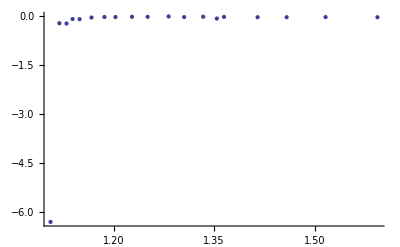

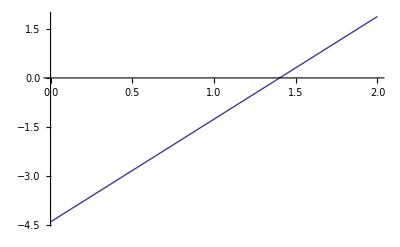

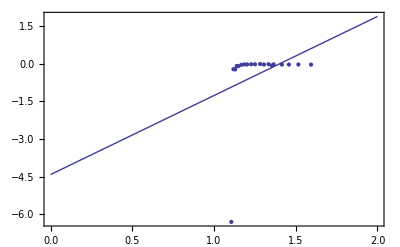

```mathematica
line = Fit[data,{1,x},x]
DataPlot=ListPlot[data]
FitPlot=Plot[line,{x,0,2}]
Show[DataPlot,FitPlot,PlotRange->All,Frame->True,AxesOrigin->{0,0}]
```